Abs[3/(2 ξ^2)-(3 (Sin[2 ξ]+Sinh[2 ξ]))/(4 ξ^3 (Cos[2 ξ]+Cosh[2 ξ]))]

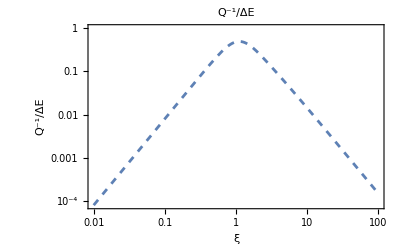

```mathematica
QNoHeatFlow =Abs[ 6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) ]
QNoHeatFlowg=LogLogPlot[QNoHeatFlow,{ξ,0.01,100},PlotLabel->"Q^-1/ΔE", Frame->True,FrameLabel->{ξ,"Q^-1/ΔE"},PlotStyle->Dashed,GridLinesStyle->LightGray,GridLines->Full]
```

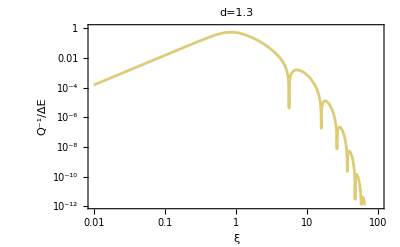

Show::gtype: Timesはグラフィックスのタイプではありません．

Show[3/4 Abs[(-2 ξ (Cos[2.3 ξ] Cosh[0.3 ξ]+Cos[0.3 ξ] Cosh[2.3 ξ])-Cosh[2.3 ξ] Sin[0.3 ξ]+Cosh[0.3 ξ] Sin[2.3 ξ]-Cos[2.3 ξ] Sinh[0.3 ξ]+Cos[0.3 ξ] Sinh[2.3 ξ])/(ξ^3 (Cos[2.6 ξ]+Cosh[2.6 ξ]))],ξ→8.3]

```mathematica
QHeatFlow13=Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{d->1.3};

QHeatFlow13g=LogLogPlot[QHeatFlow13,{ξ,0.01,100},PlotLabel->"d=1.3", Frame->True,FrameLabel->{ξ,"Q^-1/ΔE"},PlotStyle->RGBColor["#DDCC77"],GridLinesStyle->LightGray,GridLines->Full]
```

Show::gcomb: Show[{0.00126927,2.09142×10^-6,4.41159×10^-10,3.77565×10^-14}]のグラフィックスオブジェクトを組み合せることができませんでした．

Show[{0.00126927,2.09142×10^-6,4.41159×10^-10,3.77565×10^-14}]

Show::gcomb: Show[{891.24,540887.,2.5642×10^9,2.9961×10^13}]のグラフィックスオブジェクトを組み合せることができませんでした．

Show[{891.24,540887.,2.5642×10^9,2.9961×10^13}]

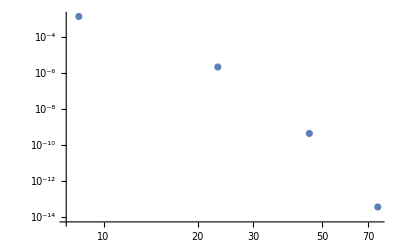

{{8.34,0.0013},{23.17,2.09×10^-6},{45.4,4.41×10^-10},{75.08,3.78×10^-14}}

```mathematica
QHeatFlow13Sapphire=Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{d->1.3,ξ->{8.34,23.17,45.40,75.08}};
Show[QHeatFlow13Sapphire]
Show[1/(0.884 QHeatFlow13Sapphire)]
QHeatFlow13Sapphireg=ListLogLogPlot[{{8.34,0.0013},{23.17,2.09 10^-6},{45.40,4.41 10^-10},{75.08,3.78 10^-14}}]
SapphireList={{8.34,0.0013},{23.17,2.09 10^-6},{45.40,4.41 10^-10},{75.08,3.78 10^-14}}
```

Show::gcomb: Show[{0.00127271,2.11712×10^-6,4.52594×10^-10,3.90922×10^-14}]のグラフィックスオブジェクトを組み合せることができませんでした．

Show[{0.00127271,2.11712×10^-6,4.52594×10^-10,3.90922×10^-14}]

Show::gcomb: Show[{1964.31,1.18085×10^6,5.52372×10^9,6.39514×10^13}]のグラフィックスオブジェクトを組み合せることができませんでした．

Show[{1964.31,1.18085×10^6,5.52372×10^9,6.39514×10^13}]

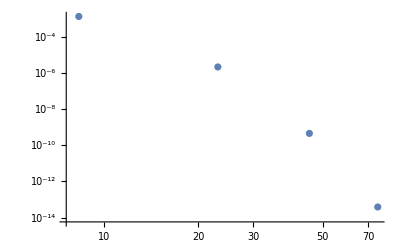

{{8.33,0.0013},{23.15,2.12×10^-6},{45.37,4.53×10^-10},{75.01,3.91×10^-14}}

```mathematica
QHeatFlow13Silicon=Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{d->1.3,ξ->{8.33,23.15,45.37,75.01}};
Show[QHeatFlow13Silicon]
Show[1/(0.4 QHeatFlow13Silicon)]
QHeatFlow13Silicong=ListLogLogPlot[{{8.33,0.0013},{23.15,2.12 10^-6},{45.37,4.53 10^-10},{75.01,3.91 10^-14}}]
SiliconList={{8.33,0.0013},{23.15,2.12 10^-6},{45.37,4.53 10^-10},{75.01,3.91 10^-14}}
```

Show::gcomb: Show[{2.4554×10^-6,1.84122×10^-12,5.22041×10^-21,2.66415×10^-32}]のグラフィックスオブジェクトを組み合せることができませんでした．

Show[{2.4554×10^-6,1.84122×10^-12,5.22041×10^-21,2.66415×10^-32}]

Show::gcomb: Show[{12608.9,1.68148×10^10,5.93052×10^18,1.16209×10^30}]のグラフィックスオブジェクトを組み合せることができませんでした．

Show[{12608.9,1.68148×10^10,5.93052×10^18,1.16209×10^30}]

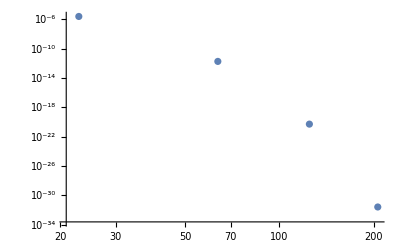

{{22.9,2.46×10^-6},{63.62,1.84×10^-12},{124.69,5.22×10^-21},{206.12,2.66×10^-32}}

```mathematica
QHeatFlow13SUS304=Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.
{d->1.3,ξ->{22.90,63.62,124.69,206.12}};
Show[QHeatFlow13SUS304]
Show[1/(32.30 QHeatFlow13SUS304)]
QHeatFlow13SUS304g=ListLogLogPlot[{{22.90,2.46 10^-6},{63.62,1.84 10^-12},{124.69,5.22 10^-21},{206.12,2.66 10^-32}}]
SUS304List={{22.90,2.46 10^-6},{63.62,1.84 10^-12},{124.69,5.22 10^-21},{206.12,2.66 10^-32}}
```

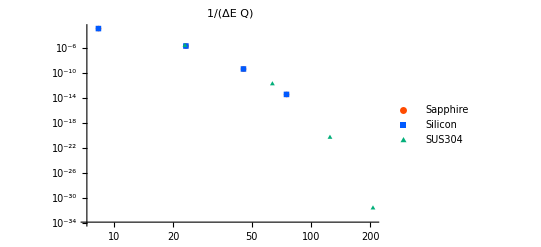

```mathematica
List3=ListLogLogPlot[{SapphireList,SiliconList,SUS304List},PlotLabel->Q^-1/ΔE,FrameLabel->{ξ,"Q^-1/ΔE"},PlotLegends->Placed[{Sapphire, Silicon,SUS304},{0.25,0.3}],PlotMarkers->{{●,10},{■,10},{▲,10}},PlotStyle->{RGBColor["#FF4B00"],RGBColor["#005aff"],RGBColor["#03af7a"]},GridLinesStyle->LightGray,GridLines->Full]
```

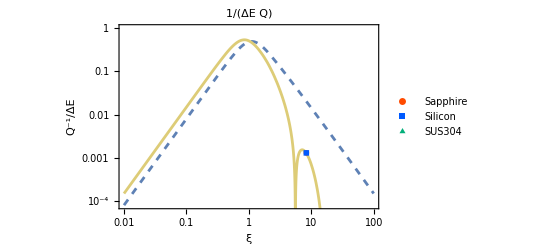

```mathematica
Show[{QNoHeatFlowg,QHeatFlow13g,List3}]
```